```mathematica
data=ToExpression[Import["F:\\Project\\HeisenbergModel\\Debug\\Original data\\B="<>ToString@#<>"_D="<>ToString@2.44949<>"_Step_1000.vector"]]&/@{0,2,4};
```

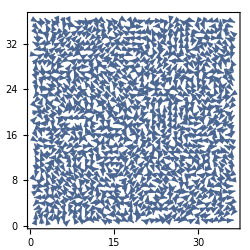
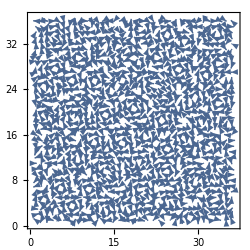
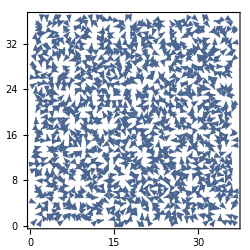

```mathematica
Parallelize[ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorPoints->36,ImageSize->250]&/@data]
```

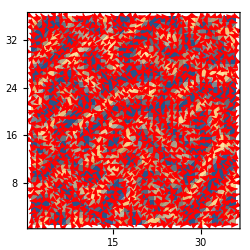
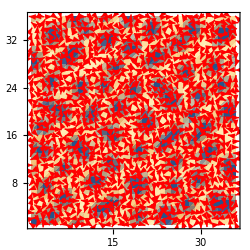
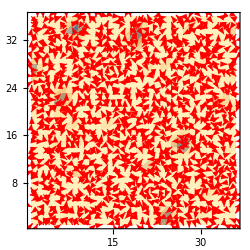

```mathematica
Parallelize[Show[
ListDensityPlot[#/.{x_,y_,z_}->z,PlotRange->{-2,2},ColorFunctionScaling->False],
ListVectorPlot[#/.{x_,y_,z_}->{x,y},VectorStyle->Red,VectorPoints->36]
,ImageSize->250]&/@data]
```

```mathematica
data1=Table[
Table[{i,j,data⟦ii⟧⟦i⟧⟦j⟧},{i,1,36},{j,1,36}],
{ii,1,3}];
```

```mathematica
Parallelize@Table[
Graphics3D[
{Thick,Arrowheads[0.008],({Arrow[{{#1⟦1⟧,#1⟦2⟧,0},{#1⟦1⟧+#1⟦3,1⟧,#1⟦2⟧+#1⟦3,2⟧,#1⟦3,3⟧}}]}&)/@Flatten[data1⟦k⟧,1]},
Axes->True,BoxRatios->{10,10,1},(*AspectRatio->1,*)ImageSize->Large]
,{k,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}